```mathematica
raw={{40,0.685371,0.661495,8.73322*10^-09},{39.5,0.686737,0.663272,7.85051*10^-11},{39,0.687955,0.664949,3.08186*10^-16},{38.5,0.689012,0.666517,1.22002*10^-21},{38,0.689893,0.667965,7.89349*10^-24},{37.5,0.690579,0.669282,2.73853*10^-29},{37,0.691051,0.670456,1.67854*10^-31},{36.5,0.69129,0.671472,5.42853*10^-37},{36,0.691271,0.672318,1.81583*10^-42},{35.5,0.690971,0.672976,5.87291*10^-48},{35,0.690359,0.67343,1.83905*10^-53},{34.5,0.689407,0.673661,5.57664*10^-59},{34,0.68808,0.673649,1.63807*10^-64},{33.5,0.686339,0.673371,4.66219*10^-70},{33,0.684144,0.672803,3.618*10^-72},{32.5,0.681448,0.67192,2.05994*10^-74},{32,0.678199,0.670692,4.19176*10^-78},{31.5,0.674339,0.669088,2.78033*10^-80},{31,0.669804,0.667074,3.88659*10^-82},{30.5,0.664521,0.664614,8.66929*10^-88},{30,0.658409,0.661666,1.99845*10^-93},{29.5,0.651378,0.658185,1.32818*10^-95},{29,0.643326,0.654126,1.63658*10^-97},{28.5,0.634137,0.649435,8.73495*10^-100},{28,0.623683,0.644056,1.74486*10^-105},{27.5,0.611819,0.637929,3.47059*10^-111},{27,0.598386,0.630989,6.67454*10^-117},{26.5,0.583206,0.623163,1.24718*10^-122},{26,0.566089,0.614382,6.1969*10^-125},{25.5,0.546836,0.604568,3.19691*10^-128},{25,0.525255,0.593655,1.37691*10^-130},{24.5,0.501189,0.581541,2.22001*10^-136},{24,0.474564,0.568185,3.61465*10^-142},{23.5,0.445467,0.553526,1.82187*10^-144},{23,0.414255,0.537534,2.01373*10^-146},{22.5,0.381631,0.520217,1.18856*10^-148},{22,0.348622,0.501642,6.10278*10^-151},{21.5,0.316357,0.48195,9.92908*10^-157},{21,0.285756,0.461357,2.99935*10^-161},{20.5,0.257324,0.440195,3.20089*10^-164},{20,0.231167,0.418845,1.07861*10^-167},{19.5,0.207121,0.397727,1.10452*10^-173},{19,0.184882,0.377203,3.30691*10^-176},{18.5,0.164093,0.357574,3.21641*10^-182},{18,0.144377,0.339022,3.79848*10^-188},{17.5,0.12533,0.321635,4.21085*10^-194},{17,0.106482,0.305377,4.56205*10^-200},{16.5,0.0871815,0.290228,1.16812*10^-202},{16,0.0662491,0.276097,1.56645*10^-206},{15.5,0.0402755,0.262886,3.22375*10^-209},{15,1.52224*10^-09,0.2505,2.39965*10^-212},{14.5,4.29141*10^-11,0.238847,1.6502*10^-218},{14,1.81293*10^-13,0.227842,1.61193*10^-224},{13.5,3.08317*10^-16,0.217406,1.3965*10^-230},{13,2.82737*10^-19,0.207471,1.20271*10^-236},{12.5,1.61958*10^-22,0.197974,9.98955*10^-243},{12,6.33646*10^-26,0.188859,8.07002*10^-249},{11.5,1.79813*10^-29,0.18008,6.32431*10^-255},{11,3.86426*10^-33,0.171584,4.81118*10^-261},{10.5,6.49631*10^-37,0.163339,3.55158*10^-267},{10,8.76101*10^-41,0.155299,2.5442*10^-273}};
```

```mathematica
makeSeries:=Table[Table[{raw[[j]][[1]],raw[[j]][[1+i]]},{j,1,Length[raw]}],{i,1,3}]
```

```mathematica
table[pairs_]:=Grid[Transpose[pairs],Spacings->{3,0}];
```

```mathematica
fm2[name_String,size_,opacity_]:=ResourceFunction["PolygonMarker"][name,Offset@size,{Dynamic@EdgeForm[{CurrentValue["Color"],Opacity[opacity]}],Dynamic@FaceForm@Lighter[CurrentValue["Color"],0.75]}];
```

```mathematica
markers={fm2["Square",0.4*20,1.0],fm2["Diamond",0.4*17,1.0],fm2["ThreePointedStar",0.4*11,1.0]};
```

```mathematica
ν=0.35
```

0.35

```mathematica
Romero[w_]:=18.2(1-ν)Sqrt[1+ν]+14.5 w
```

```mathematica
Romero[0.1]
```

15.1952

```mathematica
makePlot[romero_]:=Show[ListPlot[makeSeries,PlotMarkers->markers,Joined->True,PlotRange->All,Frame->True,ImageSize->Large,FrameTicksStyle->Directive[20],PlotLegends->Placed[PointLegend[ConstantArray["",3],LabelStyle->20,LegendLayout->table,LegendMargins->{{0,0},{-30,0}},LegendMarkerSize->{80,50}],Above]],Graphics[{Black,Thick,Dotted,InfiniteLine[{romero,0},{0,1}]}]]
```

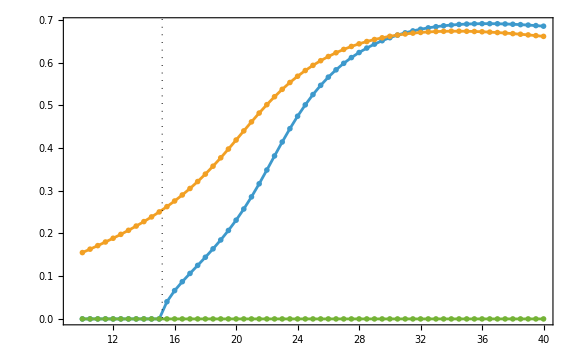

```mathematica
plt = makePlot[Romero[0.1]]
```

```mathematica
Export[NotebookDirectory[]<>"W-0.1.pdf",plt]
```

C:\Users\evoug\Documents\Projects\lateralbuckling\plots\W-0.1.pdf